# Rapport projekt 1

Magnus Fredriksson, TIDAB, magfred@kth.se
Fredrik Öberg, TIDAB, fobe@kth.se

Uppgift 1: Polynomekvation

## Sammanfattning

### Uppgift

Uppgiften bestod i att hitta lösningarna till polynomekvationen

	 x^5-2 x^4-19/4 x^3+31/4 x^2+11/2 x-15/2=0
	 
samt att också rita grafen för polynomet och markera nollställena med en röd punkt.

### Resultat

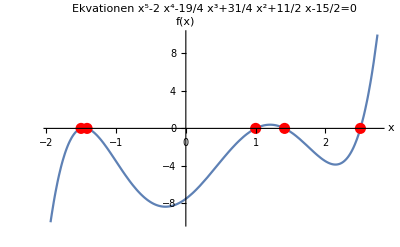
Låt f[x] vara en funktion av polynomet och när f[x] = 0 gavs dessa x-värden för polynomets nollställen i en lista

{-3/2,1,5/2,-√2,√2}

Dessa värden markerades ut i en graf av polynomet och slutresultatet blev som följer:

	-Graphics-

## Kod

```mathematica
f[x_]=x^5-2 x^4-19/4 x^3+31/4 x^2+11/2 x-15/2;
```

```mathematica
{x1, x2, x3, x4, x5}=x/.Solve[f[x]==0];
```

```mathematica
Plot[
f[x], {x, -5, 5},
PlotRange->{{3,-3},{-10,10}},
AxesLabel->{"x", "f(x)"}, 
PlotLabel->"Ekvationen x^5-2 x^4-19/4 x^3+31/4 x^2+11/2 x-15/2=0",
Epilog->{
Red, PointSize[0.02], 
Point[{{x1, f[x1]},{x2, f[x2]}, {x3, f[x3]},{x4, f[x4]},{x5, f[x5]}}]}
];
```

Uppgift 2: Ekvation med absolutbelopp

## Sammanfattning

### Uppgift

Lös ekvationen |x-1|+|x+2|=3. Illustrera lösningsområdet grafiskt

### Resultat

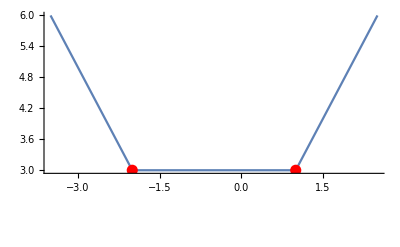
Funktionen Reduce användes där ekvationen |x-1|+|x+2|=3 matades in. Detta gav följande lösningsområde:
		
		-2≤x≤1  

Lösningsområdet visualiserades grafiskt genom att använda funktionen Plot. Lösningsområdet markerades tydligt med en röd färg för att kontrastera mot den blåa som användes för grafen.	

-Graphics-

## Kod

```mathematica
solution = Reduce[{Abs[x-1]+Abs[x+2] == 3}, x, Reals];
pPlot = 
 Plot[{Abs[x-1]+Abs[x+2]},{x, -10,10 },
PlotRange->{{-5,5},{0,6}},
Epilog->{
Red,
Thick,
PointSize[.02],
Line[{{-2,2.5},{1,2.5}}],
Line[{{-2,3},{-2,2.5}}],
Line[{{1,3},{1,2.5}}],
Point[{{-2,3},{1,3}}],
Black,
Text[Style[solution,16],{-1,2}]
}];
Show[pPlot,PlotRange->All];
```

Uppgift 3: Binomisk ekvation

## Sammanfattning

### Uppgift

Uppgiftens instruktioner var att finna lösningen till ekvationen z^7= 1 - i och visa grafiskt att dessa ligger på en cirkel i komplexa talplanet.

### Resultat

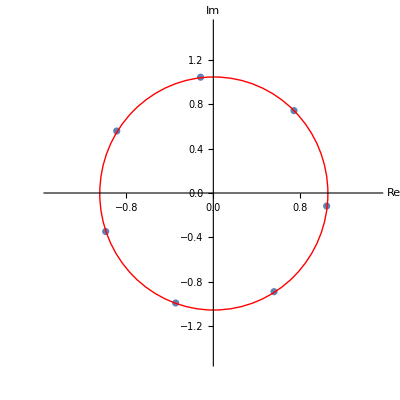
Ekvationen löstes genom att använda funktionen Solve vilket gav följande komplexa tal:

	{(1-ⅈ)^(1/7),-(-1)^(1/7) (1-ⅈ)^(1/7),(-1)^(2/7) (1-ⅈ)^(1/7),-(-1)^(3/7) (1-ⅈ)^(1/7),    
(-1)^(4/7) (1-ⅈ)^(1/7),-(-1)^(5/7) (1-ⅈ)^(1/7),(-1)^(6/7) (1-ⅈ)^(1/7)} 
	
	
En lista skapades genom funktionen Table där de reella talen sorterades från de imaginära och sedan tilldelades ett numeriskt värde. Genom att använda värdena i den skapade listan i funktionen ListPlot visualiserades punkterna för lösningarna till ekvationen. Därefter sammanbands punkterna med en cirkel för att visualisera att lösningarna för ekvationen låg på en cirkel i det komplexa planet.
-Graphics-

## Kod

```mathematica
Z=z /. Solve[z^7==1-I];
```

```mathematica
table =Table[{N[Re[Z⟦i⟧]], N[Im[Z⟦i⟧]]}, {i, 1, Length[Z]}];
```

```mathematica
ListPlot[table, AspectRatio->1,PlotRange->{{-1.5,1.5},{-1.5, 1.5}},AxesLabel->{"Re", "Im"}, Epilog->{ Red, Circle[{0,0},Abs[Z⟦1⟧]]}];
```

Uppgift 4: Akilles och sköldpaddan

## Sammanfattning

### Uppgift

I paradoxen “Akilles och sköldpaddan” har Akilles en hastighet som är 10 gånger så hög som sköldpaddan som startar 80 meter före Akilles. Paradoxalt nog kommer dock aldrig Akilles ifatt sköldpaddan enligt tankesättet i paradoxen. Uppgiften bestod i att undersöka och förklara denna paradox, samt ta fram en lösning för när Akilles faktiskt kommer i kapp sköldpaddan och visa detta  både numeriskt och grafiskt

### Numerisk Lösning

När Akilles kommer till sköldpaddans utgångsposition  har sköldpaddan rört sig en viss sträcka.
När Akilles rör sig mot sköldpaddans nya position har återigen förflyttat sig en viss sträcka. Denna sträcka är dock mindre än den ursprungliga sträckan och på detta sätt minskar alltid avståndet mellan sköldpaddan och Akilles utan att riktigt bli 0.

I första iterationen behöver Akilles röra sig:

80/10^0 m

Under tiden har sköldpaddan tagit sig 80/10 m, Akilles behöver då ta sig framåt 

80/10^1 m

Under denna tid har sköldpaddan tagit sig 80/10^2 m, Akilles behöver då ta sig framåt ytterligare

80/10^2 m

o.s.v. 

Eftersom distansintervallet snabbt blir väldigt litet (sträckan närmar sig 0, när iterationerna närmar sig oändlighet), kan vi anta att det är ett ändligt avstånd som Akilles ska röra sig, även om antalet iterationer är oändligt.
Notera även att eftersom Akilles och sköldpaddans hastigheter är konstant, och sträckan närmar sig 0, närmar  sig även tiden som det tar Akilles att springa sträckan 0. 
Sträckan Akilles därmed behöver ta sig för att faktiskt komma ikapp sköldpaddan kan därmed skrivas som summan av en oändlig serie avtagande värden:


∑_n^(0→∞) tortoiseHeadstart/10^n

800/9

Paradoxen för greken Zenon - som var den person som myntade denna paradox - låg i att de gamla grekerna inte hade ett koncept kallat oändlighet, vilket vi idag använder när vi pratar om gränsvärden. På det sättet kan vi lösa detta och liknande problem, vilket de gamla grekerna alltså inte kunde.

### Grafisk Lösning

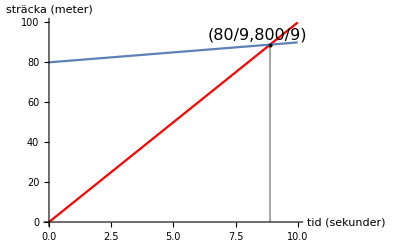
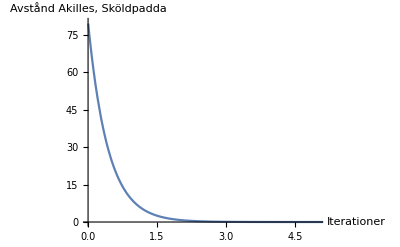
Akilles och sköldpaddans mötespunkt kan bestämmas grafiskt genom att visualisera då Akilles och sköldpaddans graf antar samma värde. Antar vi  att sköldpaddans hastighet är 1m/s och Akilles är 10m/s får vi följande graf:


-Graphics-

I Mathematica kan man finna denna punkt genom att lösa ekvationen då funktionen för sköldpaddans sträcka ger samma värde som funktionen för Akilles sträcka.

Vi kan också visualisera avståndet mellan Akilles och sköldpaddan som en graf där x-axeln representerar antalet iterationer Akilles sprungit.
Den här grafen illustrerar varför paradoxen uppstår; avståndet blir snabbt nästan lika med 0, men Akilles kommer till synes inte ifatt.


-Graphics-

## Kod

```mathematica
HoldForm[Sum[(tortoiseHeadstart/(10^n)),{n,0->Infinity}]];
AkillesDistance = Sum[tortoiseHeadstart/(10^n),{n,0,∞}];
```

```mathematica
tortoiseHeadstart= 80;
akil[x_] = 10x;
tort[x_] = tortoiseHeadstart+x;
{x1 }=x/.Solve[akil[x] ==tort[x]];
PlotAkil = Plot[akil[x], {x, 0, 10}, 
PlotStyle->{Red},
Epilog -> {Gray,
Line[{{x1, 0},{x1, akil[x1]}}],
Black,
Text[Style["("<>ToString[TraditionalForm[x1]]<>"," <> ToString[TraditionalForm[akil[x1]]] <>")",16,FontFamily->Times],{x1-0.5,akil[x1]+5}],
PointSize[Large],
Point[{x1, akil[x1]}]
}];
PlotTort = Plot[tort[x], {x, 0, 10}];
Show[PlotAkil, PlotTort, PlotRange->{{0, 10},{0,100}},AxesLabel->{"tid (sekunder)", "sträcka (meter)"},ImageSize->{Large}];
```

```mathematica
distance[x_]= tortoiseHeadstart/(10^x);
distancePlot = Plot[distance[x],{x,-1.63,10}];
Show[distancePlot, 
PlotRange->{{0,5},{0,80}},
AxesLabel->{"Iterationer", "Avstånd Akilles, Sköldpadda"},
ImageSize->{Large}
];
```